In this notebook we try to find an obvious manifestation of Rydberb blockade.

## Some definitions

```mathematica
Sn[N_,S_]:=N*S^N/N!*Exp[-S]
Sbin[N0_,N_,S_]:=N*(S/N0)^N*(1-S/N0)^(N0-N)*N0!/(N!*(N0-N)!)
L[A_,Γ_,t0_]:=A/(1+Γ (t-t0)^2)
G[A_,σ_,t0_]:=A/(2Pi σ)* Exp[-(t-t0)^2/(2 σ^2)]
```

## Cooking data

### Importation of the two files: Forster resonance ON and Forster OFF

#### Reading the files

```mathematica
col=1 ;(*color selection*)
A25=Import["A25.tsv"];A26=Import["A26.tsv"];
```

#### Parsing the files. We consider the sum of signal on channel P and S, as suggested by Igor

```mathematica
i=1;f=200;
SS=A25[[i;;f,12]]+A25[[i;;f,18]];
S1=A25[[i;;f,7]]+A25[[i;;f,13]];
S2=A25[[i;;f,8]]+A25[[i;;f,14]];
S3=A25[[i;;f,9]]+A25[[i;;f,15]];
S4=A25[[i;;f,10]]+A25[[i;;f,16]];
S5=A25[[i;;f,11]]+A25[[i;;f,17]];

SSn=A26[[i;;f,12]]+A26[[i;;f,18]];
S1n=A26[[i;;f,7]]+A26[[i;;f,13]];
S2n=A26[[i;;f,8]]+A26[[i;;f,14]];
S3n=A26[[i;;f,9]]+A26[[i;;f,15]];
S4n=A26[[i;;f,10]]+A26[[i;;f,16]];
S5n=A26[[i;;f,11]]+A26[[i;;f,17]];
```

#### Creating the graphs for each number of atoms

```mathematica
GSS=ListPlot[SS,Joined->True,PlotStyle->ColorData[col,"ColorList"][[2]]];
GS1=ListPlot[S1,Joined->True,PlotStyle->ColorData[col,"ColorList"][[3]]];
GS2=ListPlot[S2,Joined->True,PlotStyle->ColorData[col,"ColorList"][[4]]];
GS3=ListPlot[S3,Joined->True,PlotStyle->ColorData[col,"ColorList"][[5]]];
GS4=ListPlot[S4,Joined->True,PlotStyle->ColorData[col,"ColorList"][[6]]];
GS5=ListPlot[S5,Joined->True,PlotStyle->ColorData[col,"ColorList"][[7]]];

GSSn=ListPlot[SSn,Joined->True,PlotStyle->ColorData[col,"ColorList"][[2]]];
GS1n=ListPlot[S1n,Joined->True,PlotStyle->ColorData[col,"ColorList"][[3]]];
GS2n=ListPlot[S2n,Joined->True,PlotStyle->ColorData[col,"ColorList"][[4]]];
GS3n=ListPlot[S3n,Joined->True,PlotStyle->ColorData[col,"ColorList"][[5]]];
GS4n=ListPlot[S4n,Joined->True,PlotStyle->ColorData[col,"ColorList"][[6]]];
GS5n=ListPlot[S5n,Joined->True,PlotStyle->ColorData[col,"ColorList"][[7]]];
```

### Analysis of the data

#### Fitting the total signal on a Lorentzian

```mathematica
FSS=FindFit[SS,L[A,Γ,t0],{A,Γ,t0},t,MaxIterations->10000]
FSSn=FindFit[SSn,L[A,Γ,t0],{A,Γ,t0},t,MaxIterations->10000]
(*FSS=FindFit[SS,G[A,Γ,t0],{A,Γ,t0},t,MaxIterations->10000]*) (* There is no large profit using a gaussian instead of a lorentzian *)
```

{A→0.903012,Γ→0.00874229,t0→98.9096}

{A→1.18862,Γ→0.0121193,t0→79.9893}

#### Comparing the data with the rescaling of the total signal using the binomial distribution for each number of atom

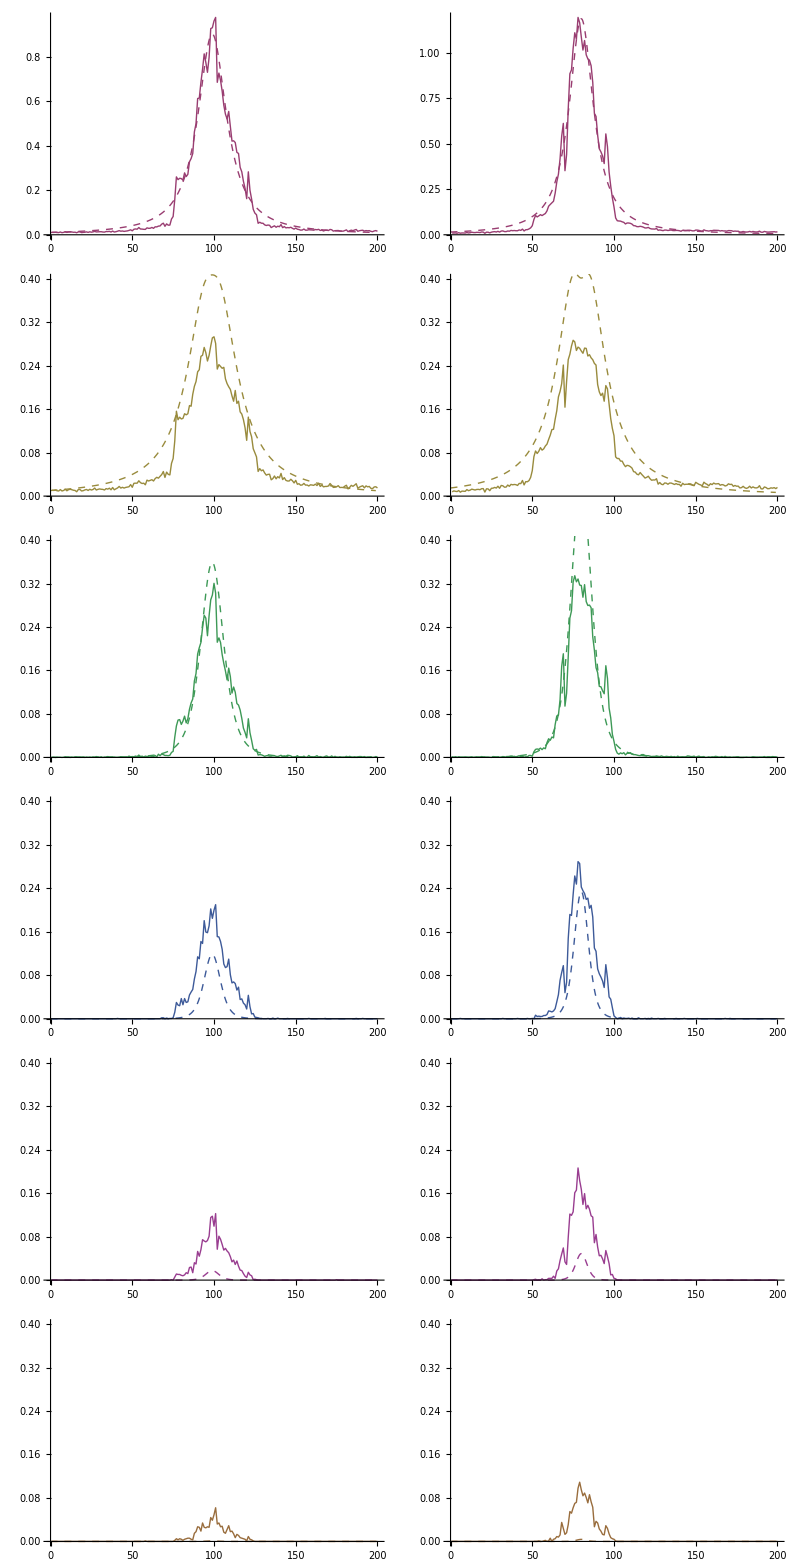

```mathematica
N0=5; (* We assume the total number of atoms in the interaction volume is N0=5 *)

GFSS=Plot[L[A,Γ,t0]/.FSS,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[2]],Thick,Dashed]];
GFS1=Plot[Sbin[N0,1,L[A,Γ,t0]]/.FSS,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[3]],Thick,Dashed]];
GFS2=Plot[Sbin[N0,2,L[A,Γ,t0]]/.FSS,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[4]],Thick,Dashed]];
GFS3=Plot[Sbin[N0,3,L[A,Γ,t0]]/.FSS,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[5]],Thick,Dashed]];
GFS4=Plot[Sbin[N0,4,L[A,Γ,t0]]/.FSS,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[6]],Thick,Dashed]];
GFS5=Plot[Sbin[N0,5,L[A,Γ,t0]]/.FSS,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[7]],Thick,Dashed]];

GFSSn=Plot[L[A,Γ,t0]/.FSSn,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[2]],Thick,Dashed]];
GFS1n=Plot[Sbin[N0,1,L[A,Γ,t0]]/.FSSn,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[3]],Thick,Dashed]];
GFS2n=Plot[Sbin[N0,2,L[A,Γ,t0]]/.FSSn,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[4]],Thick,Dashed]];
GFS3n=Plot[Sbin[N0,3,L[A,Γ,t0]]/.FSSn,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[5]],Thick,Dashed]];
GFS4n=Plot[Sbin[N0,4,L[A,Γ,t0]]/.FSSn,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[6]],Thick,Dashed]];
GFS5n=Plot[Sbin[N0,5,L[A,Γ,t0]]/.FSSn,{t,0,f-i},PlotRange->All,PlotStyle->Directive[ColorData[col,"ColorList"][[7]],Thick,Dashed]];

Grid[Transpose[{{Show[GSS,GFSS,PlotRange->{0,Max[SS]},ImageSize->Medium],
Show[GS1,GFS1,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS2,GFS2,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS3,GFS3,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS4,GFS4,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS5,GFS5,PlotRange->{0,0.4},ImageSize->Medium]},
{Show[GSSn,GFSSn,PlotRange->{0,Max[SSn]},ImageSize->Medium],
Show[GS1n,GFS1n,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS2n,GFS2n,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS3n,GFS3n,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS4n,GFS4n,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS5n,GFS5n,PlotRange->{0,0.4},ImageSize->Medium]}
}]]
```

#### Plotting two Rydberg blockade criteria (these quantities should be always equal to zero)

0

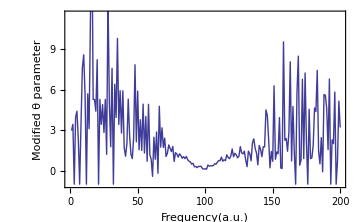
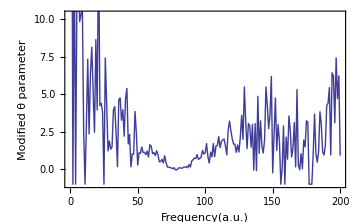
-Graphics- | -Graphics-
Forster ON | Forster OFF

```mathematica
Sbin[N0,2,S]/Sbin[N0,1,S]*(N0-S)/(S*(N0-1))-1//Simplify (* first criterion: verification that this is really equal to zero *)
Grid[{{ListPlot[S2/S1*(N0-SS)/(SS*(N0-1)) - 1,Joined->True,ImageSize->Medium,Frame->True,FrameLabel->{{"Modified θ parameter",None},{"Frequency(a.u.)",None}},LabelStyle->Bold],ListPlot[S2n/S1n*(N0-SSn)/(SSn*(N0-1)) - 1,Joined->True,ImageSize->Medium,Frame->True,FrameLabel->{{"Modified θ parameter",None},{"Frequency(a.u.)",None}},LabelStyle->Bold]},{"Forster ON","Forster OFF"}}]
```

0

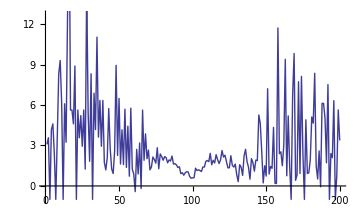
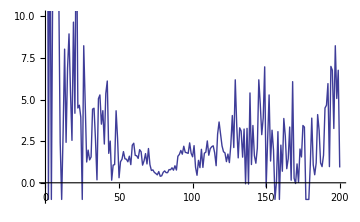
-Graphics- | -Graphics-
Forster ON | Forster OFF

```mathematica
Sbin[N0,2,S]/Sbin[N0,1,S]^2*(1-S/N0)^N0/(1-1/N0) -1//Simplify (* second criterion: verification that this is really equal to zero *)
Grid[{{ListPlot[S2/S1^2*(1-SS/N0)^N0/(1-1/N0) - 1,Joined->True,ImageSize->Medium],ListPlot[S2n/S1n^2*(1-SSn/N0)^N0/(1-1/N0) - 1,Joined->True,ImageSize->Medium]},{"Forster ON","Forster OFF"}}]
```

### Dealing with mean data (taking the even and the odd parts of the spectra)

```mathematica
ff=99*2+1; (* we have select the right size of the spectrum, 99 is the maximum*)
S1e=(S1[[i;;ff]]+Reverse[S1[[i;;ff]]])/2; (*the even part is the sum of the original spectrum and the reversed spectrum*)
S2e=(S2[[i;;ff]]+Reverse[S2[[i;;ff]]])/2;
S3e=(S3[[i;;ff]]+Reverse[S3[[i;;ff]]])/2;
S4e=(S4[[i;;ff]]+Reverse[S4[[i;;ff]]])/2;
S5e=(S4[[i;;ff]]+Reverse[S5[[i;;ff]]])/2;
SSe=(SS[[i;;ff]]+Reverse[SS[[i;;ff]]])/2;

S1o=(S1[[i;;ff]]-Reverse[S1[[i;;ff]]])/2; (*the odd part is the difference between the original spectrum and the reversed spectrum*)
S2o=(S2[[i;;ff]]-Reverse[S2[[i;;ff]]])/2;
S3o=(S3[[i;;ff]]-Reverse[S3[[i;;ff]]])/2;
S4o=(S4[[i;;ff]]-Reverse[S4[[i;;ff]]])/2;
S5o=(S5[[i;;ff]]-Reverse[S5[[i;;ff]]])/2;
SSo=(SS[[i;;ff]]-Reverse[SS[[i;;ff]]])/2;

ffn=80*2+1;
S1en=(S1n[[i;;ffn]]+Reverse[S1n[[i;;ffn]]])/2;
S2en=(S2n[[i;;ffn]]+Reverse[S2n[[i;;ffn]]])/2;
S3en=(S3n[[i;;ffn]]+Reverse[S3n[[i;;ffn]]])/2;
S4en=(S4n[[i;;ffn]]+Reverse[S4n[[i;;ffn]]])/2;
S5en=(S5n[[i;;ffn]]+Reverse[S5n[[i;;ffn]]])/2;
SSen=(SSn[[i;;ffn]]+Reverse[SSn[[i;;ffn]]])/2;

S1on=(S1n[[i;;ffn]]-Reverse[S1n[[i;;ffn]]])/2;
S2on=(S2n[[i;;ffn]]-Reverse[S2n[[i;;ffn]]])/2;
S3on=(S3n[[i;;ffn]]-Reverse[S3n[[i;;ffn]]])/2;
S4on=(S4n[[i;;ffn]]-Reverse[S4n[[i;;ffn]]])/2;
S5on=(S5n[[i;;ffn]]-Reverse[S5n[[i;;ffn]]])/2;
SSon=(SSn[[i;;ffn]]-Reverse[SSn[[i;;ffn]]])/2;
```

#### Plotting the even parts for 1 and 2 atoms (these graphs are even)

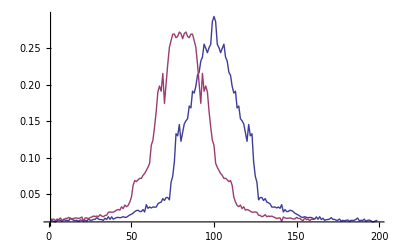

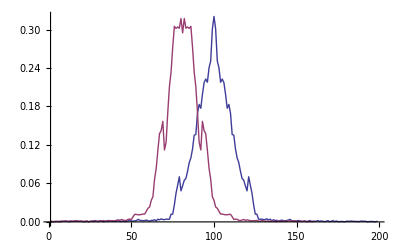

```mathematica
ListPlot[{S1e,S1en},PlotRange->All,Joined->True]
ListPlot[{S2e,S2en},PlotRange->All,Joined->True]
```

#### Plotting the odd part for 1 and 2 atoms (the graph must be null)

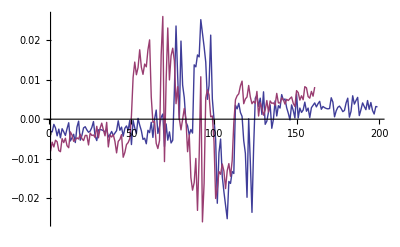

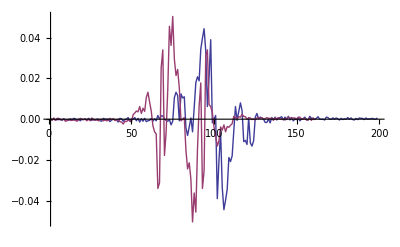

```mathematica
ListPlot[{S1o,S1on},PlotRange->All,Joined->True]
ListPlot[{S2o,S2on},PlotRange->All,Joined->True]
```

#### Plotting the even and the odd part for the total signal (Forester ON and OFF)

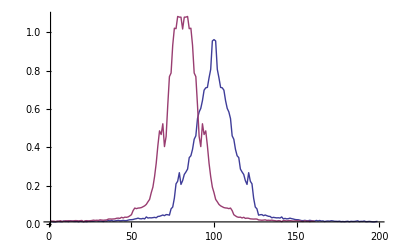

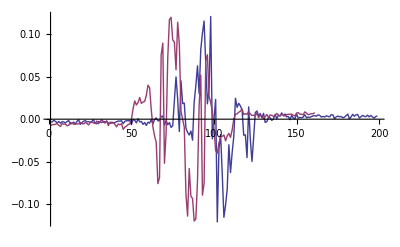

```mathematica
ListPlot[{SSe,SSen},PlotRange->All,Joined->True]
ListPlot[{SSo,SSon},PlotRange->All,Joined->True]
```

#### Comparing the even part of the data with the rescaling of the total signal using the binomial distribution for each number of atom (

```mathematica
GSSe=ListPlot[SSe,Joined->True,PlotStyle->ColorData[col,"ColorList"][[2]]];
GS1e=ListPlot[S1e,Joined->True,PlotStyle->ColorData[col,"ColorList"][[3]]];
GS2e=ListPlot[S2e,Joined->True,PlotStyle->ColorData[col,"ColorList"][[4]]];
GS3e=ListPlot[S3e,Joined->True,PlotStyle->ColorData[col,"ColorList"][[5]]];
GS4e=ListPlot[S4e,Joined->True,PlotStyle->ColorData[col,"ColorList"][[6]]];
GS5e=ListPlot[S5e,Joined->True,PlotStyle->ColorData[col,"ColorList"][[7]]];

GSSen=ListPlot[SSen,Joined->True,PlotStyle->ColorData[col,"ColorList"][[2]]];
GS1en=ListPlot[S1en,Joined->True,PlotStyle->ColorData[col,"ColorList"][[3]]];
GS2en=ListPlot[S2en,Joined->True,PlotStyle->ColorData[col,"ColorList"][[4]]];
GS3en=ListPlot[S3en,Joined->True,PlotStyle->ColorData[col,"ColorList"][[5]]];
GS4en=ListPlot[S4en,Joined->True,PlotStyle->ColorData[col,"ColorList"][[6]]];
GS5en=ListPlot[S5en,Joined->True,PlotStyle->ColorData[col,"ColorList"][[7]]];
```

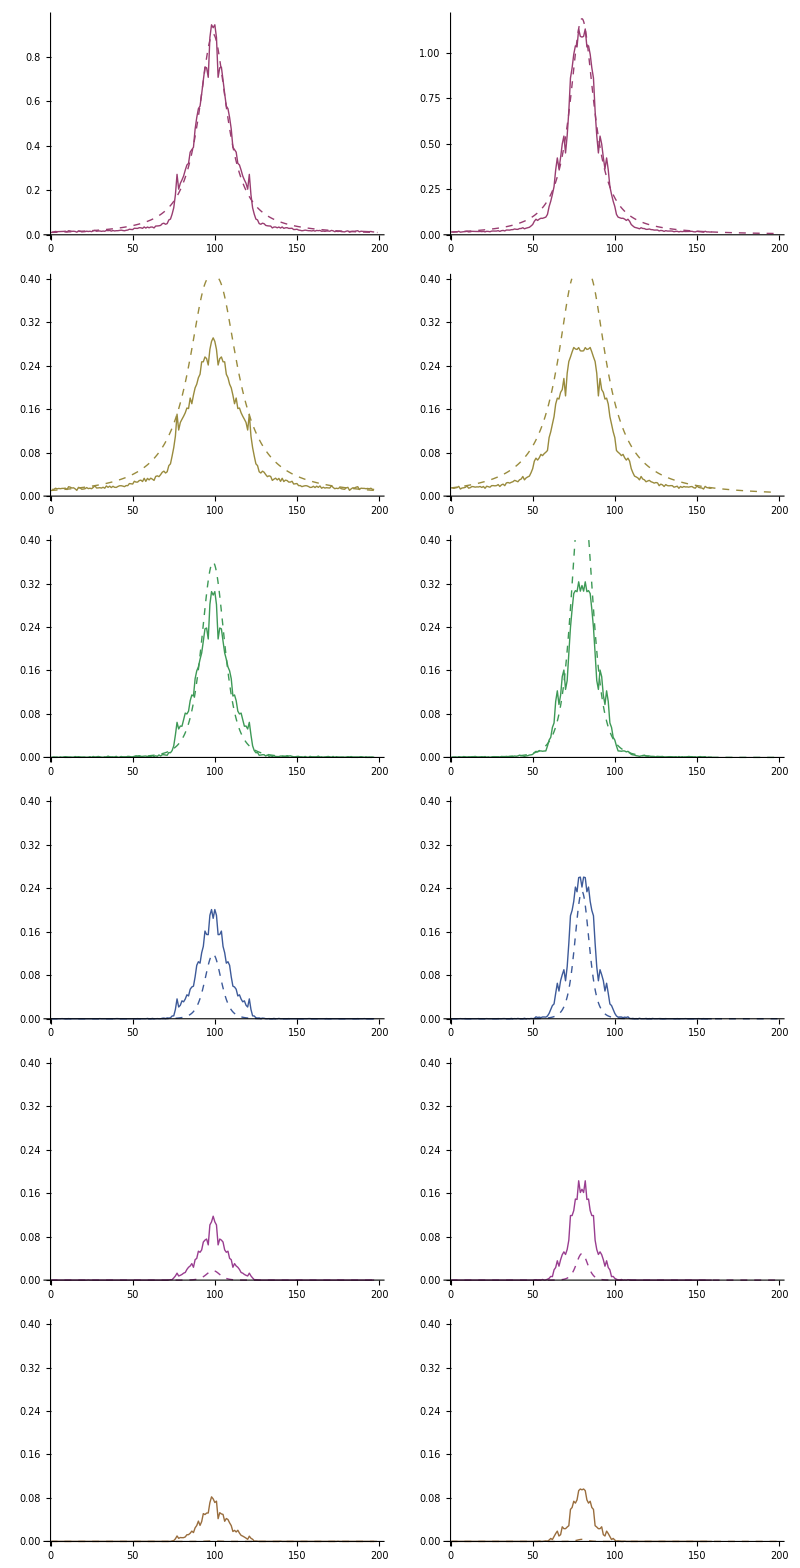

```mathematica
Grid[Transpose[{{Show[GSSe,GFSS,PlotRange->{0,Max[SS]},ImageSize->Medium],
Show[GS1e,GFS1,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS2e,GFS2,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS3e,GFS3,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS4e,GFS4,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS5e,GFS5,PlotRange->{0,0.4},ImageSize->Medium]},
{Show[GSSen,GFSSn,PlotRange->{0,Max[SSn]},ImageSize->Medium],
Show[GS1en,GFS1n,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS2en,GFS2n,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS3en,GFS3n,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS4en,GFS4n,PlotRange->{0,0.4},ImageSize->Medium],
Show[GS5en,GFS5n,PlotRange->{0,0.4},ImageSize->Medium]}
}]]
```

#### Plotting the two previous Rydberg blockade criteria with the even part of the spectra

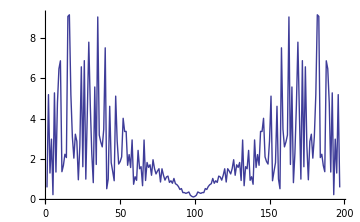
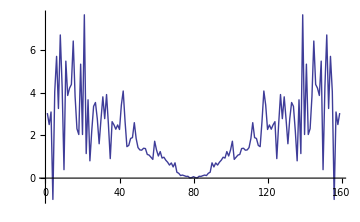
-Graphics- | -Graphics-
Forster ON | Forster OFF

```mathematica
Grid[{{ListPlot[S2e/S1e*(N0-SSe)/(SSe*(N0-1)) - 1,Joined->True,ImageSize->Medium],ListPlot[S2en/S1en*(N0-SSen)/(SSen*(N0-1)) - 1,Joined->True,ImageSize->Medium]},{"Forster ON","Forster OFF"}}]
```

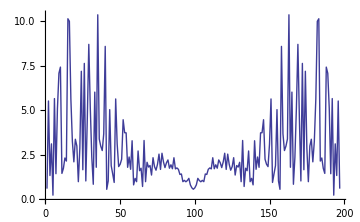
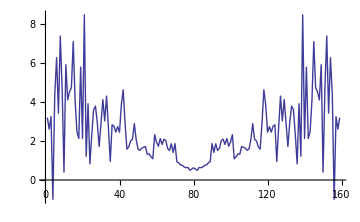
-Graphics- | -Graphics-
Forster ON | Forster OFF

```mathematica
Grid[{{ListPlot[S2e/S1e^2*(1-SSe/N0)^N0/(1-1/N0) - 1,Joined->True,ImageSize->Medium],ListPlot[S2en/S1en^2*(1-SSen/N0)^N0/(1-1/N0) - 1,Joined->True,ImageSize->Medium]},{"Forster ON","Forster OFF"}}]
```

### Reproducing the graph on the poster

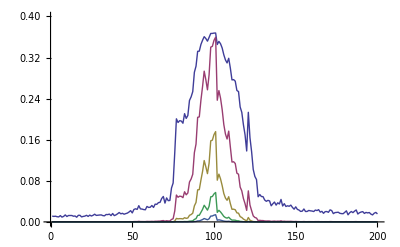

```mathematica
ListPlot[Table[N*SS^N*Exp[-SS]/N!,{N,1,5}],Joined->True,PlotRange->{0,0.4}]
```

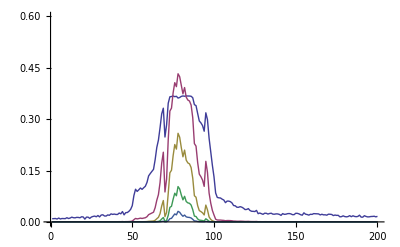

```mathematica
ListPlot[Table[N*SSn^N*Exp[-SSn]/N!,{N,1,5}],Joined->True,PlotRange->{0,0.6}]
```